```mathematica
f[{x_,y_}]:={(2x-4)y-8, (2y-x)(2y+x)}
Df[{x_,y_}]:=({{2 y, -4+2 x}, {-2 x, 2 (-x+2 y)+2 (x+2 y)}})
CPs=NSolveValues[f[{x,y}]=={0,0},{x,y},Reals]
Table[
A=Df[CP];
{λs,vs}=Eigensystem[A];
λs,
{CP,CPs}
]
```

{{4.,2.},{-2.,-1.}}

{{12.,8.},{-5.+4.79583 ⅈ,-5.-4.79583 ⅈ}}

{{4.,2.},{-2.,-1.},{1.-2.64575 ⅈ,-0.5+1.32288 ⅈ},{1.+2.64575 ⅈ,-0.5-1.32288 ⅈ}}

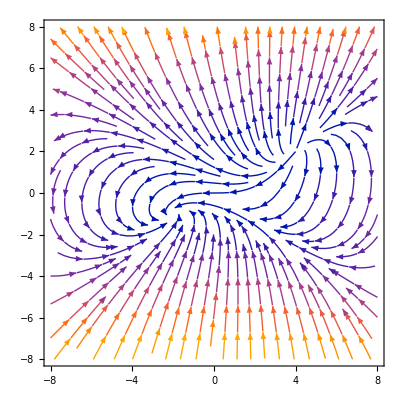

```mathematica
NSolveValues[f[{x,y}]=={0,0},{x,y}]
StreamPlot[ f[{x,y}],{x,-8,8},{y,-8,8}]
```